## MEASUREMENT OF REFRACTIVE INDICES OF NEON, ARGON, KRYPTON AND XENON IN THE 253.7-140.4nm WAVELENGTH RANGE. DISPERSION RELATIONS AND ESTIMATED OSCILLATOR STRENGTHS OF THE RESONANCE LINES A. Bideau-Mehu et al, J. Quant. Spectrosc. Radiat. Transfer 25, 395-402(1981)

The constant factor in the formula of  molecular polarizability Nq_e^2/(12 π^2 ϵ_0 m_e c^2) in unit of μm^-2 for 1 mole gas at STP

```mathematica
((6.02214 10^23)/(22.413969545014 10^-3)(1.60217662 10^-19)^2)/(12 π^2 8.8541878128×10^-12 9.10938370 10^-31 299792458^2)/(10^-6)^-2
```

0.00803328

For gases, the refractive index is close to 1, so that there are a constant factor as Nq_e^2/(8 π^2 ϵ_0 m_e c^2)

```mathematica
((6.02214 10^23)/(22.413969545014 10^-3)(1.60217662 10^-19)^2)/(8 π^2 8.8541878128×10^-12 9.10938370 10^-31 299792458^2)/(10^-6)^-2
```

0.0120499

The relative difference between 1980s SI units and updated SI units

```mathematica
(0.012055-%)/0.012055
```

0.00042181

The molecular polarizability term of argon gases at STP where wavelength in unit of um

```mathematica
alphaGasArgonum[x_]:=1.2055 10^-2(0.2075/(91.012-x^-2)+0.0415/(87.892-x^-2)+4.3330/(214.02-x^-2))
```

nm to um convertor

The wavelength in unit of nm

```mathematica
wavelength[x_]:=√(1/x)10^3
```

```mathematica
wavelength[91.012]
```

104.822

```mathematica
wavelength[87.892]
```

106.666

```mathematica
wavelength[214.02]
```

68.3554

```mathematica
nmTOum[x_]:=x 10^-3
```

The molecular polarizability of argon gases at STP where wavelength in unit of nm

```mathematica
alphaGasArgonnm[x_]:=alphaGasArgonum[nmTOum[x]]
```

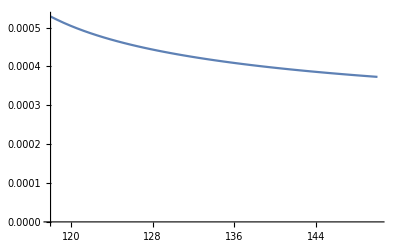

```mathematica
Plot[alphaGasArgonnm[x],{x,118,150},AxesOrigin->{118,0}]
```

The molecular polarizability term of liquid argon  at 86.8 K where wavelength in unit of um

```mathematica
alphaLiquidArgonum[x_]:=1.2055 10^-2 2/3 21.1 10^27/((6.02214 10^23)/(22.413969545014 10^-3))(0.2075/(91.012-x^-2)+0.0415/(87.892-x^-2)+4.3330/(214.02-x^-2))
```

```mathematica
wavelength[91.012]
```

104.822

```mathematica
wavelength[87.892]
```

106.666

The molecular polarizability term of liquid argon  at 86.8 K where wavelength in unit of nm

```mathematica
alphaLiquidArgonnm[x_]:=alphaLiquidArgonum[nmTOum[x]]
```

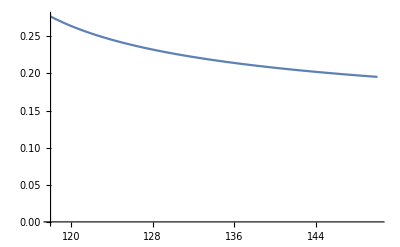

```mathematica
Plot[alphaLiquidArgonnm[x],{x,118,150},AxesOrigin->{118,0}]
```

The molecular polarizability term concern excitons of liquid argon  at 86.8 K where wavelength in unit of um

```mathematica
alphaLiquidArgonExcitonum[x_]:=1.2055 10^-2 2/3 21.1 10^27/((6.02214 10^23)/(22.413969545014 10^-3))(0.207/(94.2596-x^-2)+0.054/(90.1869-x^-2)+4.3330/(214.02-x^-2))
```

The molecular polarizability term concern excitons of liquid argon  at 86.8 K where wavelength in unit of nm

```mathematica
alphaLiquidArgonExcitonnm[x_]:=alphaLiquidArgonExcitonum[nmTOum[x]]
```

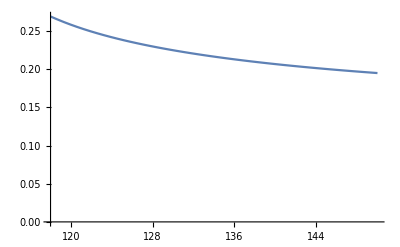

```mathematica
Plot[alphaLiquidArgonExcitonnm[x],{x,118,150},AxesOrigin->{118,0}]
```

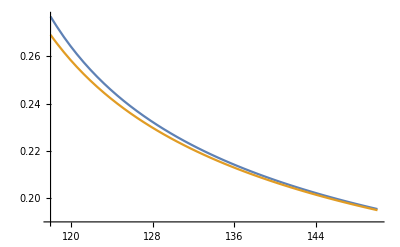

```mathematica
Plot[{alphaLiquidArgonnm[x],alphaLiquidArgonExcitonnm[x]},{x,118,150},AxesOrigin->{118,0.19}]
```

The refractive index of liquid argon  at 86.8 K where wavelength in unit of nm

```mathematica
nLiquidArgon[x_]:=√((2 alphaLiquidArgonnm[x]+1)/(1-alphaLiquidArgonnm[x]))
```

The refractive index  concern excitons of liquid argon  at 86.8 K where wavelength in unit of nm

```mathematica
nLiquidArgonExciton[x_]:=√((2 alphaLiquidArgonExcitonnm[x]+1)/(1-alphaLiquidArgonExcitonnm[x]))
```

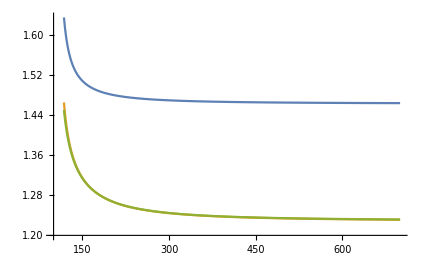

```mathematica
Plot[{n[nmTOeV[x]],nLiquidArgon[x],nLiquidArgonExciton[x]},{x,118,700},AxesOrigin->{100,1.2}]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

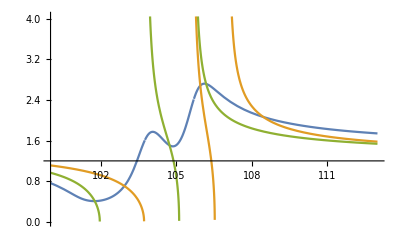

```mathematica
Plot[{n[nmTOeV[x]],nLiquidArgon[x],nLiquidArgonExciton[x]},{x,100,113},AxesOrigin->{100,1.2}]
```

```mathematica
nLiquidArgon[128]
```

1.38104

```mathematica
nLiquidArgonExciton[128]
```

1.37657

```mathematica
nLiquidArgon[643.9]
```

1.2318

```mathematica
nLiquidArgonExciton[643.9]
```

1.23224

The complex dielectric constant

```mathematica
eepsilon[x_]:=(2 (1.2055 10^-2 2/3 21.1 10^27/((6.02214 10^23)/(22.413969545014 10^-3))(0.207/(94.2596-x^-2-ⅈ 0.112918 x^-1)+0.054/(90.1869-x^-2-ⅈ 0.12098/□ x^-1)+4.3330/(214.02-x^-2)))+1)/(1-(1.2055 10^-2 2/3 21.1 10^27/((6.02214 10^23)/(22.413969545014 10^-3))(0.207/(94.2596-x^-2-ⅈ 0.112918 x^-1)+0.054/(90.1869-x^-2-ⅈ 0.12098 x^-1)+4.3330/(214.02-x^-2))))
```

The real refractive index calculated from the complex dielectric constant

```mathematica
nnn[x_]:=√((Re[eepsilon[x]]+√(Re[eepsilon[x]]^2+Im[eepsilon[x]]^2))/2)
```

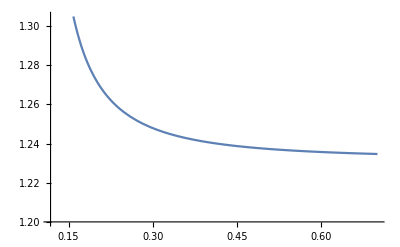

```mathematica
Plot[nnn[x],{x,0.118, 0.7},AxesOrigin->{0.118,1.2}]
```

```mathematica
nnn[0.128]
```

1.3765

```mathematica
nnn[0.11271290]
```

1.54301

```mathematica
nnn[643.9]
```

1.23193

The real part of the complex dielectric constant where wavelength in unit of um

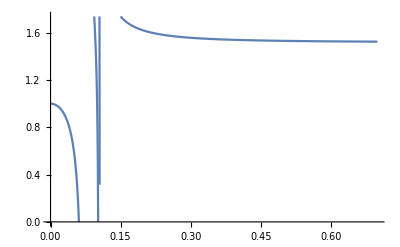

```mathematica
Plot[Re[eepsilon[x]],{x,0.0 ,0.7},AxesOrigin->{0.0,0.0}]
```

The imaginary part of the complex dielectric constant where wavelength in unit of um

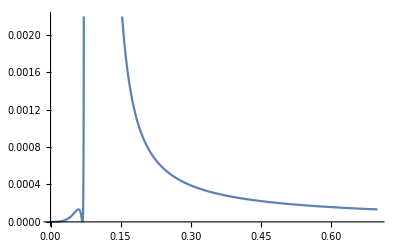

```mathematica
Plot[Im[eepsilon[x]],{x,0.0,0.7},AxesOrigin->{0.0,0.0}]
```

The real part of the complex dielectric constant where wavelength in unit of eV

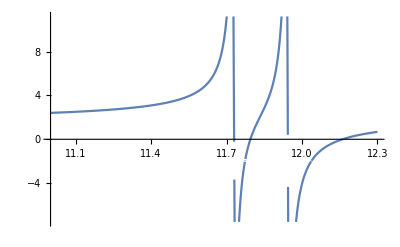

```mathematica
Plot[Re[eepsilon[eVTOnm[x]/1000]],{x,11.0,12.3}]
```

The imaginary part of the complex dielectric constant where wavelength in unit of eV

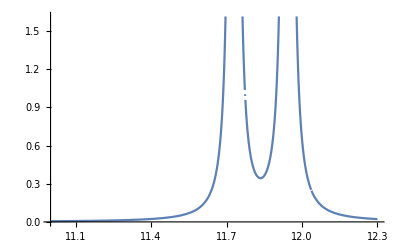

```mathematica
Plot[Im[eepsilon[eVTOnm[x]/1000]],{x,11.0,12.3}]
```

```mathematica
kk[x_]:=Im[eepsilon[x]]/(2 √((Re[eepsilon[x]]+√(Re[eepsilon[x]]^2+Im[eepsilon[x]]^2))/2))
```

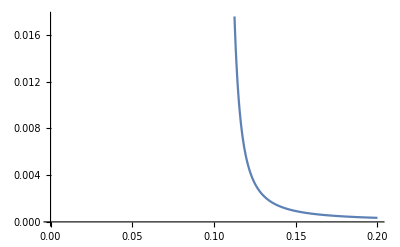

```mathematica
Plot[kk[x],{x,0.1, 0.2},AxesOrigin->{0.0,0}]
```

The imaginary refractive index of 128 nm

```mathematica
kk[0.128]
```

0.00261174

The imaginary refractive index of 700 nm

```mathematica
kk[0.7]
```

0.0000541698

The absorption length of 128nm in unit of m

```mathematica
(128 10^-9)/(4 π kk[0.128])
```

3.84054×10^-6